# Euler Problem 18

## Maximum path sum I

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.

That is, 3 + 7 + 4 + 9 = 23.

Find the maximum total from top to bottom of the triangle below:

```mathematica
page=Import["https://projecteuler.net/problem=18"];
Column[triangle=Flatten[StringSplit[#," "]&/@StringSplit[StringTrim@StringCases[page,"\n"~~a:"75"~~triangle__~~"\nNOTE":>a<>triangle],"\n"],1]]
```

{75}
{95,64}
{17,47,82}
{18,35,87,10}
{20,04,82,47,65}
{19,01,23,75,03,34}
{88,02,77,73,07,63,67}
{99,65,04,28,06,16,70,92}
{41,41,26,56,83,40,80,70,33}
{41,48,72,33,47,32,37,16,94,29}
{53,71,44,65,25,43,91,52,97,51,14}
{70,11,33,28,77,73,17,78,39,68,17,57}
{91,71,52,38,17,14,91,43,58,50,27,29,48}
{63,66,04,68,89,53,67,30,73,16,69,87,40,31}
{04,62,98,27,23,09,70,98,73,93,38,53,60,04,23}

NOTE: As there are only 16384 routes, it is possible to solve this problem by trying every route. However, Problem 67, is the same challenge with a triangle containing one-hundred rows; it cannot be solved by brute force, and requires a clever method! ;o)

## Make Matrix/Graph

```mathematica
padRow[row_List]:=Block[
{
g
},
ArrayPad[row,Ceiling[(15-Length[row])/2]]
]
```

```mathematica
padRow/@triangle//Grid
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 95 | 64 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 17 | 47 | 82 | 0 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 0 | 18 | 35 | 87 | 10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 20 | 04 | 82 | 47 | 65 | 0 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 0 | 19 | 01 | 23 | 75 | 03 | 34 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 88 | 02 | 77 | 73 | 07 | 63 | 67 | 0 | 0 | 0 | 0 | 
0 | 0 | 0 | 0 | 99 | 65 | 04 | 28 | 06 | 16 | 70 | 92 | 0 | 0 | 0 | 0
0 | 0 | 0 | 41 | 41 | 26 | 56 | 83 | 40 | 80 | 70 | 33 | 0 | 0 | 0 | 
0 | 0 | 0 | 41 | 48 | 72 | 33 | 47 | 32 | 37 | 16 | 94 | 29 | 0 | 0 | 0
0 | 0 | 53 | 71 | 44 | 65 | 25 | 43 | 91 | 52 | 97 | 51 | 14 | 0 | 0 | 
0 | 0 | 70 | 11 | 33 | 28 | 77 | 73 | 17 | 78 | 39 | 68 | 17 | 57 | 0 | 0
0 | 91 | 71 | 52 | 38 | 17 | 14 | 91 | 43 | 58 | 50 | 27 | 29 | 48 | 0 | 
0 | 63 | 66 | 04 | 68 | 89 | 53 | 67 | 30 | 73 | 16 | 69 | 87 | 40 | 31 | 0
04 | 62 | 98 | 27 | 23 | 09 | 70 | 98 | 73 | 93 | 38 | 53 | 60 | 04 | 23 |

Make unique vertex IDs?

```mathematica
nodeList=Flatten@MapIndexed[Table[node[#2[[1]],i],{i,Length[#1]}]&,triangle[[;;-2]]];
```

```mathematica
nodes={};
edges={};
makeNeighbours[parent:node[row_,column_]]:=Block[
{

},

AppendTo[nodes,{
Rule[node[row+1,column+1],triangle[[row+1,column+1]]],
If[column==1,Rule[node[row+1,1],triangle[[row+1,1]]],Rule[node[row+1,column],triangle[[row+1,column]]]]
}];
AppendTo[edges,
{parent->node[row+1,column+1],
parent->If[column==1,node[row+1,1],node[row+1,column]]}];

]
```

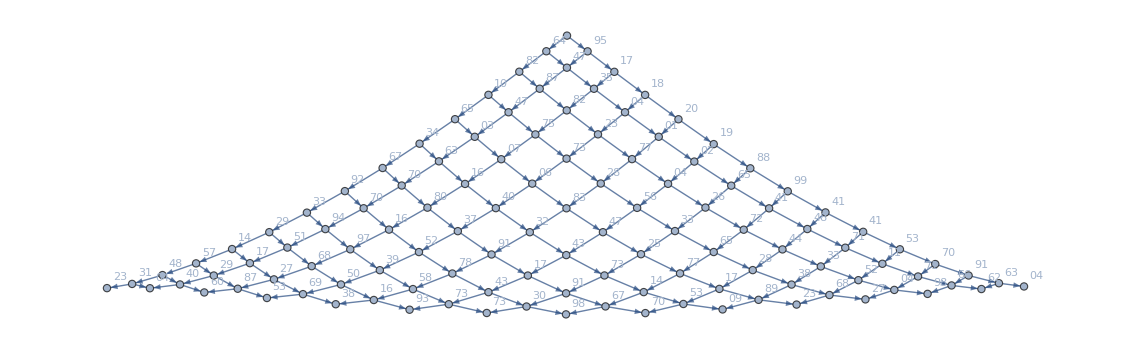

```mathematica
Map[makeNeighbours[#]&,Flatten@nodeList];
Graph[Flatten[edges],VertexLabels->Union@Flatten[nodes]]
```

```mathematica
DirectedGraph
```

```mathematica
KaryTree
```

## Breadth vs Depth First

It is preferable in tree searching problems to use breadth first scanning, as depth first requires back-tracking. In Breadth first scanning all nodes at a particular level are explored before proceeding to the next level.

For many, this is simplified to simply starting from the base of the triangle - making the best decisions at the end of the algorithm. However, an efficient implementation does not care about direction.

Visualise a smaller triangle using CompleteKaryTree: